```mathematica
<<MeshIO`
```

```mathematica
<<Render`
```

```mathematica
<<MeshOptimizePN`
```

```mathematica
mesh=ImportMesh["~/Downloads/research/weber14/models/grid2x2_L0.26.obj"];
```

```mathematica
meshData=Import["~/Downloads/research/weber14/models/grid2x2_L0.26.obj","Table"];
```

```mathematica
(*res=Import["~/MEGAsync/winshare/bunny1-2k.mx"];*)
```

```mathematica
resMesh=ImportMesh["~/Downloads/research/weber14/models/grid2x2_L0.26_result.obj"];
```

```mathematica
vt=Select[meshData,Length[#]>0&&#⟦1⟧=="vt"&]⟦All,2;;⟧;
```

```mathematica
render[{vt,mesh⟦2⟧}]
```

```mathematica
Length/@resMesh
```

{9,8}

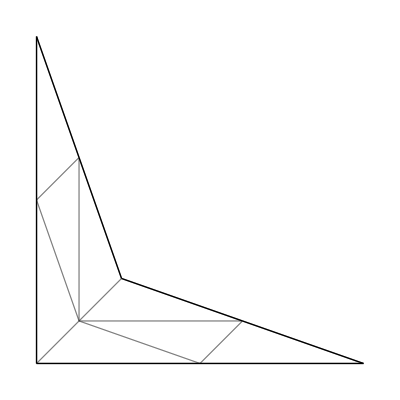

```mathematica
render[resMesh]
```

```mathematica
(*MeshToMeshRegion[mesh]*)
```

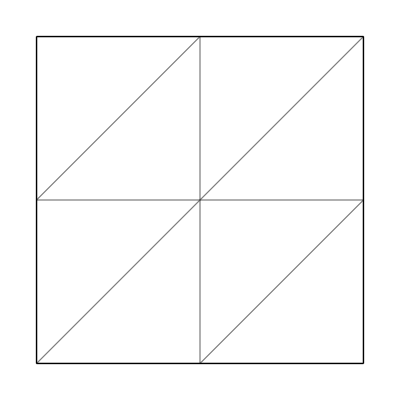

```mathematica
render[{mesh⟦1,All,;;2⟧,mesh⟦2⟧}]
```

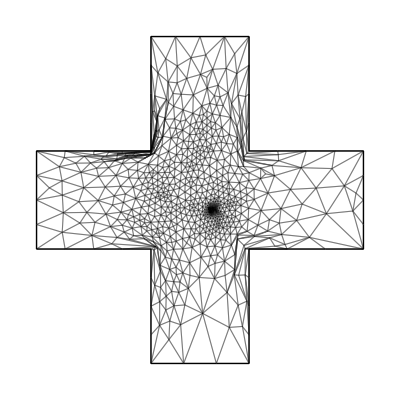

```mathematica
render[res["resMesh"]]
```

#### write obj with uv map

```mathematica
{restmesh,initmesh,handles}=Import["~/OneDrive - Washington University in St. Louis/injective-mapping-data/mx/2D_ParamExamples/Tutte/bunny1-2k.mx"];
```

```mathematica
render[restmesh]
```

-Graphics-

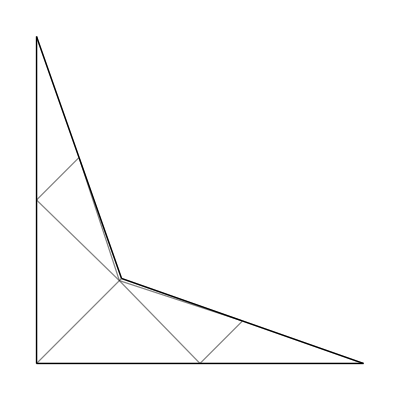

```mathematica
render[initmesh]
```

```mathematica
ExportMeshWithUV["~/Downloads/research/weber14/models/bunny1-2k-good.obj",restmesh,initmesh];
```

```mathematica
(*mesh=gridMesh[{2,2}];
mesh={N[mesh⟦1⟧],mesh⟦2⟧};*)
```

```mathematica
restmesh=mesh;
(*initmesh={N@tutteMesh⟦1⟧,tutteMesh⟦2⟧};*)
initmesh=res["resMesh"];
```